#### Example 2

```mathematica
(*Datos del problema*)
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
MatrixForm[-A]
Eigenvalues[-A]
B={{-2,1,0},{-1,-2,0},{0,1,6}};
MatrixForm[B]
Eigenvalues[B]
MatrixForm[Inverse[-A].B]
N[Eigenvalues[Inverse[-A].B]]
```

(-20 | 4 | 0
4 | -20 | 0
0 | 0 | -10)

{-24,-16,-10}

(-2 | 1 | 0
-1 | -2 | 0
0 | 1 | 6)

{6,-2+ⅈ,-2-ⅈ}

(11/96 | -1/32 | 0
7/96 | 3/32 | 0
0 | -1/10 | -3/5)

{-0.6,0.104167+0.0465847 ⅈ,0.104167-0.0465847 ⅈ}

Cálculo del field of values

-Graphics-

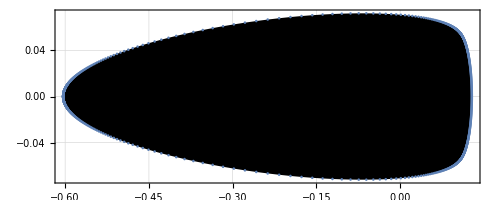

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
(*Código F()*)
RangNum[matriz_?SquareMatrixQ,t_?NumericQ]/;Internal`EffectivePrecision[matriz]<∞||InexactNumberQ[t]:=Module[{tm,v},tm=(#+ConjugateTranspose[#])/2&[matriz Exp[I t]];
v=Quiet[Check[First[Eigenvectors[tm,1,Method->{"Arnoldi","Criteria"->"RealPart"}]],MaximalBy[Transpose[Eigensystem[tm]],First][[1,-1]],Eigenvectors::arall]];
(Conjugate[v].matriz.v)/(Conjugate[v].v)];

fovOut[A_,k_]:=Module[{valPropA,θ,H,λ,δ,q,j,verticesOut = {}},
valPropA =Eigenvalues[A];
(*Cálculo de F(A) si A es hermitiana*)
If[A== ConjugateTranspose[A], 
Show[Region[ConvexHullRegion[{ReIm[Max[valPropA]],ReIm[Min[valPropA]]}, Frame->True,GridLines->Automatic,   GridLinesStyle->Dashed]], ListPlot[ReIm[valPropA]]],
(*Cálculo de F(A) si A es normal*)
  If[ A . ConjugateTranspose[A] == ConjugateTranspose[A] . A, 
    Show[Region[ConvexHullRegion[ReIm[valPropA], Frame->True,GridLines->Automatic,   GridLinesStyle->Dashed]], ListPlot[ReIm[valPropA]]],
(*Cálculo de Subscript[F, Out](A,Δ)*)
θ[i_]:= (i-1)(2 Pi /k); 
H[i_]:=N[(1/2.) (E^(I θ[i]) A + ConjugateTranspose[ E^(I θ[i]) A])];
λ[i_]:= Max[Eigenvalues[H[i]]];
δ[i_]:=θ[i+1]-θ[i];
q[i_]:= E^(-I θ[i]) (λ[i]+(λ[i] Cos[δ[i]]- λ[i+1])/Sin[δ[i]] I);
For[j=1, j<=k, j++, AppendTo[verticesOut, q[j]]];

Show[Region[ConvexHullRegion[ReIm[verticesOut], Frame->True,GridLines->Automatic,   GridLinesStyle->Red]], ListPlot[ReIm[verticesOut]]
]]]];

M=Inverse[-A].B;
autovalores=Eigenvalues[N[M]];
v=Table[ReIm[RangNum[M,t]],{t,0,2Pi}];
vect=AppendTo[v,ReIm[RangNum[M,0]]];
FAB=ListLinePlot[vect,Joined->True,PlotStyle->Blue,Filling->Axis];
 FAB2=fovOut[ M,1000]; 

circ=ParametricPlot[0.604*ReIm[E^(I*t)],{t,0,2 π},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{Blue, Orange},{"F((-A)^-1B)","D(0,r)"}],{0.75,0.0}], PlotRange->All];
Show[circ,FAB2]
FAB2
```

```mathematica
r=0.604;
```

RESTRICCIÓN TAMAÑO DE PASO IMEX BDF2

```mathematica
f21[r_]:=Solve[1+(-3-r^2) #1^2+(2-2 r^2) #1^3+4 r^4 #1^4==0,#1][[1]][[1]][[2]]
hEstBDF2[erre_]:=Abs[f21[r]]/Max[Abs[Eigenvalues[-A]]];(*IMEX BDF2*)
hEstBDF2[r]
```

0.164762

RESTRICCIÓN TAMAÑO DE PASO IMEX BDF3

```mathematica
FuncDistCuad[z_,θ_]:=(265-66 z+18 z^2+54 (-7+2 z) Cos[θ]-27 (-5+2 z) Cos[2 θ]-22 Cos[3 θ]+12 z Cos[3 θ])/(18 z^2 (19-24 Cos[θ]+6 Cos[2 θ]));

d=Simplify[Solve[-3+(-14-12 z+72 z^2) #1+(32+12 z+216 z^2) #1^2+(94+60 z+216 z^2) #1^3+(-1357+804 z+72 z^2) #1^4==0,#1][[4]][[1]][[2]]];
Funθ4[z_]:=Sqrt[FuncDistCuad[z,θ]/.{θ->Simplify[2*ArcTan[Sqrt[d]]]}];
```

```mathematica
FindRoot[Funθ4[z]==r,{z,-1}]
```

{z→-1.43083-2.43499×10^-32 ⅈ}

```mathematica
hEstBDF3=1.4308330028571634/Max[Abs[Eigenvalues[-A]]](*IMEX BDF3*)
```

0.059618

RESOLUCIÓN MÉTODO

Queremos aplicar los métodos IMEX BDF2 e IMEX BDF3 a la EDR:       Piecewise[{{y'=-Ay(t)+By(t-1)+f(t), t≥0}, {y(t)={Cos(t),ⅇ^(-0.1t),1+t}^(t), t<0}}]
De esta forma tenemos que τ=1,    A=,    B={{-1, 1, 0}, {-1, -1, 0}, {0, 1, 4}},     Sabemos que la solución de la EDR es y(t)={Cos(t),ⅇ^(-0.1t),1+t}^(t)

```mathematica
(*Cálculo de la f tilde*)
```

```mathematica
(*Datos del problema*)
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
sol[t_]:={Cos[t],E^(-0.1t),1+t};
D[sol[t],t]+A.sol[t]-B.sol[t-1]
```

{-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)}

Resolución mediante el método IMEX BDF2

```mathematica
(*h=0.5*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/2;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[3]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{0.0143146,0.00998009,772.642}

```mathematica
(*h=0.25*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/4;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[3]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{0.00467347,0.00312615,0.000334008}

```mathematica
(*h=0.1*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/10;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[3]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{0.000833948,0.000552365,0.000042632}

```mathematica
(*h=0.05*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/20;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[3]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{0.000214566,0.000141793,9.83915×10^-6}

```mathematica
(*h=0.025*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/40;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[3]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{0.0000543419,0.0000358731,2.36226×10^-6}

```mathematica
(*h=0.01*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/100;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[3]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{8.75876×10^-6,5.77837×10^-6,3.68843×10^-7}

```mathematica
(*h=0.005*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/200;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF2=Table[{t0+j*h,sol[t0+j*h]},{j,-m-1,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
y1=N[Inverse[3/2*IdentityMatrix[3]+h*A].(2*y0-1/2*yMenos1+h*fTilde[t0+h]+h*B.(2*yMenosM-yMenosM1))];

BDF2=AppendTo[BDF2,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF2[[Length[BDF2],2]]]
```

{2.19489×10^-6,1.44772×10^-6,9.14617×10^-8}

Ratios de convergencia

```mathematica
Norm[{0.0002145655677183722,0.00014179344325668253,9.839147935508663*^-6}]
```

0.000257372

```mathematica
Norm[{2.194892861240305*^-6,1.4477234487400568*^-6,9.146168622464756*^-8}]
```

2.63094×10^-6

```mathematica
Log[0.05/0.005,0.0002573724387594566/2.63093578340531*^-6](*Ratio de convergencia con IMEX BDF2*)
```

1.99045

Resolución del método mediante BDF3

```mathematica
(*h=0.5*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/2;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[3]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{0.0109063,0.00685386,6.94335×10^80}

```mathematica
(*h=0.25*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/4;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[3]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{0.00110142,0.000685472,8.88559×10^38}

```mathematica
(*h=0.1*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/10;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[3]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{0.0000538653,0.0000329633,5.31851×10^-6}

```mathematica
(*h=0.05*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/20;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[3]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{5.93684×10^-6,3.60303×10^-6,7.05725×10^-7}

```mathematica
(*h=0.025*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/40;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[3]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{6.90359×10^-7,4.169×10^-7,9.06022×10^-8}

```mathematica
(*h=0.01*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/100;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[3]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{4.21592×10^-8,2.53751×10^-8,5.88767×10^-9}

```mathematica
(*h=0.005*)
```

```mathematica
P={{2,-2,0},{-2,-2,0},{0,0,-1/8}};
X0={{-24,0,0},{0,-16,0},{0,0,-10}};
X=P.X0.Inverse[P];
A=-X;
B={{-2,1,0},{-1,-2,0},{0,1,6}};
τ=1;
h=1/200;
m=τ/h;
t0=0;
tf=500;
nf=Round[(tf-t0)/h];
sol[t_]:={Cos[t],E^(-0.1t),1+t};
y0=sol[t0];
fTilde[t_]:={-ⅇ^(-0.1 (-1+t))-4 ⅇ^(-0.1 t)+2 Cos[1-t]+20 Cos[t]-Sin[t],2 ⅇ^(-0.1 (-1+t))+19.9 ⅇ^(-0.1 t)+Cos[1-t]-4 Cos[t],1-ⅇ^(-0.1 (-1+t))-6 t+10 (1+t)};
BDF3=Table[{t0+j*h,sol[t0+j*h]},{j,-m-2,0}];

For[i=1,i<=nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];


y1=N[Inverse[11/6*IdentityMatrix[3]+h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*fTilde[t0+h]+h*B.(3*yMenosM-3*yMenosM1+yMenosM2))];

BDF3=AppendTo[BDF3,{t0+h,y1}];
t0=t0+h;
y0=y1;
]
Abs[sol[tf]-BDF3[[Length[BDF3],2]]]
```

{5.18485×10^-9,3.11704×10^-9,7.43114×10^-10}

Ratios de convergencia

```mathematica
Norm[{5.936837211506507*^-6,3.6030322743130228*^-6,7.05724744420877*^-7}]
```

6.9804×10^-6

```mathematica
Norm[{5.184850770945104*^-9,3.117039288138919*^-9,7.431140147673432*^-10}]
```

6.09515×10^-9

```mathematica
Log[0.05/0.005,6.980395766756893*^-6/6.095148060524474*^-9](*Ratio de convergencia con IMEX BDF3*)
```

3.0589